```mathematica
(* temp globals, to be localized in the Manipulate. *)
windowHalfWidth =3 ;
mMax = 30 ;
springLatticeData ={
{Darker@Orange,1,0,0,0,0,1},
{Darker@Green,0,1,0,0,1,0},
{Darker@Purple,1,1,0,0,0,0},
{Darker@Cyan,-1,1,1,0,1,0} } ;
kMax = 0.9 ;
primaryDisplaySize = 200 ;




(* Based on a ListLinePlot version posted in: http://mathematica.stackexchange.com/a/37228/10 *)
ClearAll[springPoints] ;
springPoints::usage = "springPoints[ point1, point2, numberOfTurns, height, fractionToDrawAsLinesAtEnds ].  Example:

ListLinePlot[springPoints[{1,2},{3,5}], AspectRatio→Automatic, PlotStyle -> Darker[ Purple ] ]" ;
springPoints[ a1_List, a2_List, n_Integer:8,h_:.05, f_: 0.1 ] :=Module[{n1, d, nd, r, r1 },

n1 = Norm[a1] ;
d = a2 - a1 ;
nd = Norm[d] ;
r = RotationMatrix[ArcTan @@  d ] ;
r1 = r . {n1, 0} ;

{
Table[ a1 -r1 + r . { n1 + nd f + t (1 - 2f) nd, h Sin[ 2 Pi n t]}, {t, 0, 1, 0.01 } ],
Table[ a1 -r1 + r . { n1 + nd f + (1 - 2f) nd + t f nd, 0}, {t, 0, 1, 0.01 } ],
Table[ a1 -r1 + r . { n1 +t f nd, 0}, {t, 0, 1, 0.01 } ]
}
] ;

ClearAll[indexLable] ;
indexLable::usage = "k_i(or other character) in italic. indexLable['k', 1]" ;
indexLable = Subscript[Style[#1,Italic], #2] & ;

ClearAll[kLable] ;
kLable::usage = "k_i(or other character) in italic and colored by spring index. kLable[k]" ;
kLable = Style[ indexLable["k", #], FontColor->First[springLatticeData[[#]]] ] & ;

ClearAll[lineTable] ;
lineTable[ n_List, b_List, i_List ] :=Module[{first, second},
{first, second} = i ;
Table[
Line[
{-n[[first]]b[[first]] + j b[[second]],n[[first]]b[[first]] + j b[[second]]} 
] 
, {j, -n[[second]], n[[second]]}
]
] ;

ClearAll[ calcReciprocalBasis ] ;
calcReciprocalBasis::usage = "Return a reciprocal frame basis for a set of vectors.  This doesn't include the 2 π scaling that is common in solid state physics.  Example, displaying the desired Kronicker delta behaviour:

b = {{2,1},{-1/4, 2}} ;
g = calcReciprocalBasis[ b ] ;

{g[[1]].loc[[1]],
g[[1]].loc[[2]],
g[[2]].loc[[1]],
g[[2]].loc[[2]]}
" ;
calcReciprocalBasis[loc_List] := Inverse[ Transpose[ loc ] ] ;

ClearAll[ pointsTable ] ;
pointsTable[ mPosFirstCell_List, latticeBasis_List, numberLatticeLinesToDisplay_List ] := Table[ 
mPosFirstCell + {i,j}. latticeBasis
,{i, -numberLatticeLinesToDisplay[[1]],numberLatticeLinesToDisplay[[1]]}
,{j, -numberLatticeLinesToDisplay[[2]], numberLatticeLinesToDisplay[[2]]}
] ;

(*(* This could use some heavy optimization.  It doesn't make much sense to do all the springs separately, when one set of plot points could be calculated once for a given direction, and then just translated for the rest of the springs with that orientation.
*)
ClearAll[ springLatticePlot ] ;
springLatticePlot[ calcResults_List, {color_, iOff_Integer, jOff_Integer, iStartAdj_, jStartAdj_, iRangeAdj_Integer, jRangeAdj_Integer},springStrengthFraction_] := Module[{pt, pointsDataTable, numberLatticeLinesToDisplay},

{pt,numberLatticeLinesToDisplay}={"pointsDataTable","numberLatticeLinesToDisplay"} /. calcResults ;
pointsDataTable = pt[[1]] ; (*FIXME*)

ListLinePlot[
Flatten[Table[
springPoints[ pointsDataTable[[i,j]], pointsDataTable[[i+iOff,j + jOff]], Ceiling[8 springStrengthFraction] ],
{i, 1 + iStartAdj, numberLatticeLinesToDisplay[[1]] * 2 + iRangeAdj},
{j, 1 + jStartAdj, numberLatticeLinesToDisplay[[2]] * 2 + jRangeAdj}
], 2] ,
PlotStyle ->  color ]
];*)

ClearAll[ locDependent ] ;
locDependent::usage = "Locator dependent calculations (i.e. based on the mass positions and the unit cell basis vectors)

Example:

locDependent[{1/2,1}, {1,1/2}, {{0.1,0.2} + {1/2,1} + {1,1/2}, {0.3, 0.5} - {1/2,1} - {1,1/2}}]

Will see: {0.1,0.2}, {0.3, 0.5} ; as the mPosFirstCell values.
" ;
locDependent[a_, b_, m_List] := Module[{latticeBasis, numberLatticeLinesToDisplay,reciprocalBasis,mObliqueComponents, mPosFirstCell},
latticeBasis = {a, b} ;
numberLatticeLinesToDisplay = (Ceiling[  Abs[windowHalfWidth/ latticeBasis[[#]][[#]]]] & /@ Range[2]) ;
reciprocalBasis = calcReciprocalBasis[ latticeBasis ] ;
mObliqueComponents = Table[m[[ i ]] . reciprocalBasis[[ j ]], {i, 2}, {j, 2}] ;
mPosFirstCell = (m[[#]] - Floor[mObliqueComponents[[#]]] . latticeBasis ) & /@ Range[2] ;

{
"aLoc"->a,"bLoc"->b,"mLoc"->m,
"latticeBasis"->latticeBasis,
"latticeNorms"->(Norm[latticeBasis[[#]]] & /@ Range[2]),
"latticeUnitVectors"->(Normalize[latticeBasis[[#]]] & /@ Range[2]),
"numberLatticeLinesToDisplay"-> numberLatticeLinesToDisplay,
"reciprocalBasis"-> reciprocalBasis,
"reciprocalNorms"-> (Norm[reciprocalBasis[[#]]] & /@ Range[2]),
"mObliqueComponents"-> mObliqueComponents,
"mPosFirstCell"-> mPosFirstCell,
"pointsDataTable"-> ((pointsTable[mPosFirstCell[[#]],latticeBasis,numberLatticeLinesToDisplay]) &/@ Range[2]),
"lineTable" -> (lineTable[ numberLatticeLinesToDisplay, latticeBasis, # ] & /@ Permutations[{1,2}])
}
] ;

(*ClearAll[ plotSprings ] ;
plotSprings::usage = "" ;
plotSprings[(*kp1_, kp2_, kp3_, kp4_,*) massValue_List, calcResults_] := Module[{latticeBasis,reciprocalBasis,pointsDataTable, numberLatticeLinesToDisplay, lines},

{latticeBasis,reciprocalBasis,pointsDataTable,numberLatticeLinesToDisplay, lines}={"latticeBasis","reciprocalBasis","pointsDataTable","numberLatticeLinesToDisplay", "lineTable"} /. calcResults ;

Show[{
Graphics[{
lines
,Blue,Arrow[{{0,0}, reciprocalBasis[[#]]}] & /@ Range[2]
,Thick,Arrowheads[0.05]
,Red,Arrow[{{0,0}, latticeBasis[[#]]}] & /@ Range[2]
,Blue
,PointSize[Sqrt[massValue[[1]]/mMax/500]]
,Point[ # ] & /@ pointsDataTable[[1]]
,Green
,PointSize[Sqrt[massValue[[2]]/mMax/500]]
,Point[ # ] & /@ pointsDataTable[[2]]
}
,PlotRange -> {{-windowHalfWidth/2, windowHalfWidth}, {-windowHalfWidth/2, windowHalfWidth}}
,ImageSize->primaryDisplaySize
](*,
kp1,
kp2,
kp3,
kp4*)
}]
] ;*)

ClearAll[ projOp ] ;
projOp::usage = "given an input vector v⃗ = {v_x, v_y}, compute the projection matrix operator along the unit vector in that direction.

   projOp[{1, 0}] // MatrixForm = (1 | 0
0 | 0)
projOp[{0, 1}] // MatrixForm = (0 | 0
0 | 1)
projOp[{a,b}] // MatrixForm = (a^2/(a^2+b^2) | (a b)/(a^2+b^2)
(a b)/(a^2+b^2) | b^2/(a^2+b^2))
" ;
projOp[v_List] := {{v[[1]]^2, v[[1]]v[[2]]},{v[[1]]v[[2]], v[[2]]^2}}/(v. v) ;

ClearAll[ dynamicsMatrix ] ;
dynamicsMatrix::usage = "
The dynamics of the system are all contained in the matrix equation:

((ω^2 | 0
0 | ω^2)- dynamicsMatrix )ϵ⃗ = 0
 
where,

OverVector[u_n] = ϵ⃗ E^(I (OverVector[r_n] . q⃗ - ω t))
OverVector[r_n] = n_1 a⃗ + n_2b⃗ 

Examples:
Clear[d] 
d = dynamicsMatrix[{a_x,a_y}, {b_x,b_y}, k_1,k_2,k_3,k_4, m] ;
d[{q_x,q_y}] // MatrixForm // TraditionalForm 

Clear[d] 
d = dynamicsMatrix[ a{1, 0}, a{0, 1}, k_1,k_2,k_3,k_4, m] ;
d[{q_x,q_y}] // Factor  // MatrixForm // TraditionalForm

out: (*Cell[TextData[Cell[BoxData[
FormBox[
TagBox[
RowBox[{"(", "", GridBox[{
{
FractionBox[
RowBox[{"2", " ", 
RowBox[{"(", 
RowBox[{
RowBox[{
SubscriptBox["k", "3"], " ", 
RowBox[{
SuperscriptBox["sin", "2"], "(", 
RowBox[{
FractionBox["1", "2"], " ", 
RowBox[{"(", 
RowBox[{
RowBox[{"a", " ", 
SubscriptBox["q", "x"]}], "+", 
RowBox[{"a", " ", 
SubscriptBox["q", "y"]}]}], ")"}]}], ")"}]}], "+", 
RowBox[{
SubscriptBox["k", "4"], " ", 
RowBox[{
SuperscriptBox["sin", "2"], "(", 
RowBox[{
FractionBox["1", "2"], " ", 
RowBox[{"(", 
RowBox[{
RowBox[{"a", " ", 
SubscriptBox["q", "y"]}], "-", 
RowBox[{"a", " ", 
SubscriptBox["q", "x"]}]}], ")"}]}], ")"}]}], "+", 
RowBox[{"2", " ", 
SubscriptBox["k", "1"], " ", 
RowBox[{
SuperscriptBox["sin", "2"], "(", 
FractionBox[
RowBox[{"a", " ", 
SubscriptBox["q", "x"]}], "2"], ")"}]}]}], ")"}]}], "m"], 
FractionBox[
RowBox[{"2", " ", 
RowBox[{"(", 
RowBox[{
RowBox[{
SubscriptBox["k", "3"], " ", 
RowBox[{
SuperscriptBox["sin", "2"], "(", 
RowBox[{
FractionBox["1", "2"], " ", 
RowBox[{"(", 
RowBox[{
RowBox[{"a", " ", 
SubscriptBox["q", "x"]}], "+", 
RowBox[{"a", " ", 
SubscriptBox["q", "y"]}]}], ")"}]}], ")"}]}], "-", 
RowBox[{
SubscriptBox["k", "4"], " ", 
RowBox[{
SuperscriptBox["sin", "2"], "(", 
RowBox[{
FractionBox["1", "2"], " ", 
RowBox[{"(", 
RowBox[{
RowBox[{"a", " ", 
SubscriptBox["q", "y"]}], "-", 
RowBox[{"a", " ", 
SubscriptBox["q", "x"]}]}], ")"}]}], ")"}]}]}], ")"}]}], "m"]},
{
FractionBox[
RowBox[{"2", " ", 
RowBox[{"(", 
RowBox[{
RowBox[{
SubscriptBox["k", "3"], " ", 
RowBox[{
SuperscriptBox["sin", "2"], "(", 
RowBox[{
FractionBox["1", "2"], " ", 
RowBox[{"(", 
RowBox[{
RowBox[{"a", " ", 
SubscriptBox["q", "x"]}], "+", 
RowBox[{"a", " ", 
SubscriptBox["q", "y"]}]}], ")"}]}], ")"}]}], "-", 
RowBox[{
SubscriptBox["k", "4"], " ", 
RowBox[{
SuperscriptBox["sin", "2"], "(", 
RowBox[{
FractionBox["1", "2"], " ", 
RowBox[{"(", 
RowBox[{
RowBox[{"a", " ", 
SubscriptBox["q", "y"]}], "-", 
RowBox[{"a", " ", 
SubscriptBox["q", "x"]}]}], ")"}]}], ")"}]}]}], ")"}]}], "m"], 
FractionBox[
RowBox[{"2", " ", 
RowBox[{"(", 
RowBox[{
RowBox[{
SubscriptBox["k", "3"], " ", 
RowBox[{
SuperscriptBox["sin", "2"], "(", 
RowBox[{
FractionBox["1", "2"], " ", 
RowBox[{"(", 
RowBox[{
RowBox[{"a", " ", 
SubscriptBox["q", "x"]}], "+", 
RowBox[{"a", " ", 
SubscriptBox["q", "y"]}]}], ")"}]}], ")"}]}], "+", 
RowBox[{
SubscriptBox["k", "4"], " ", 
RowBox[{
SuperscriptBox["sin", "2"], "(", 
RowBox[{
FractionBox["1", "2"], " ", 
RowBox[{"(", 
RowBox[{
RowBox[{"a", " ", 
SubscriptBox["q", "y"]}], "-", 
RowBox[{"a", " ", 
SubscriptBox["q", "x"]}]}], ")"}]}], ")"}]}], "+", 
RowBox[{"2", " ", 
SubscriptBox["k", "2"], " ", 
RowBox[{
SuperscriptBox["sin", "2"], "(", 
FractionBox[
RowBox[{"a", " ", 
SubscriptBox["q", "y"]}], "2"], ")"}]}]}], ")"}]}], "m"]}
},
GridBoxAlignment->{"Columns" -> {{Center}}, "ColumnsIndexed" -> {}, "Rows" -> {{Baseline}}, "RowsIndexed" -> {}},
GridBoxSpacings->{"Columns" -> {
Offset[0.27999999999999997`], {
Offset[0.7]}, 
Offset[0.27999999999999997`]}, "ColumnsIndexed" -> {}, "Rows" -> {
Offset[0.2], {
Offset[0.4]}, 
Offset[0.2]}, "RowsIndexed" -> {}}], "", ")"}],
Function[BoxForm`e$, 
MatrixForm[BoxForm`e$]]], TraditionalForm]],
CellChangeTimes->{3.5990563268386803`*^9, {3.5990565758059196`*^9, 3.5990566126100254`*^9}, 3.599056660298753*^9, {3.599056905058752*^9, 3.599056911414116*^9}, 3.5990570494260097`*^9, 3.5990570802537727`*^9, {3.5990923676281567`*^9, 3.599092423296341*^9}}]]])

" ;
dynamicsMatrix[ a_List, b_List, kk1_, kk2_, kk3_, kk4_, mm_ ] := (4/mm)(
projOp[a]kk1 Sin[ a . # /2 ]^2 + projOp[b]kk2 Sin[ b . # /2 ]^2+ projOp[a + b]kk3 Sin[ (b + a) . # /2 ]^2+ projOp[b - a] kk4 Sin[ (b  -a) . # /2 ]^2) & ;

ClearAll[ frequencyPlot ] ;
frequencyPlot::usage = "frequencyPlot[ dynamicsMatrix[{1,0}, {0,1}, 8, { 2 Pi, 2 Pi }, 0.5, 0.5, 0.25, 0.25, 1][#] &, ld ]" ;
frequencyPlot[mat_, ld_, meshSz_] := Module[{eigTable, qMax, omegaPointList, range},

qMax = 2 Pi("reciprocalNorms" /. ld) ;

eigTable = Flatten[Re[Table[  {{qx, qy} ,Eigenvalues[ mat[ {qx, qy}  ] // N ]}, {qx, -qMax[[1]]/2, qMax[[1]]/2, qMax[[1]]/ meshSz}, {qy, -qMax[[2]]/2, qMax[[2]]/2, qMax[[2]]/ meshSz} ] ],1] ;

omegaPointList[nn_] := Flatten[{#[[1]],Sqrt[#[[2]]][[nn]]}]&/@ eigTable  ;

range = (Dimensions[mat[ {0,0}  ]] // First // Range) ;

ListPlot3D[ omegaPointList[#] &/@ range (*Table[{#[[1]][[1]], #[[1]][[2]], Sqrt[#[[2]][[j]]]} &/@ eigTable, {j, Range[2]}]*), PlotRange -> Full , ImageSize->primaryDisplaySize,(*ImagePadding->30,*) AxesLabel->{"q_x", "q_y"}]
] ;

ClearAll[ calcDynamics ] ;
calcDynamics[calcResults_List, dynmatrix_,ql_List] := Module[{reciprocalNorms, q, eigensystem},

{reciprocalNorms}={"reciprocalNorms"} /. calcResults ;

q=(2 Pi ql[[#]]reciprocalNorms[[#]] &/@ Range[2]) ;

eigensystem = ({Sqrt[#[[1]]], #[[2]]}&/@(Eigensystem[ dynmatrix[q] ] // Transpose)) ;

{q, eigensystem}
] ;

ClearAll[ showDynamics ] ;
showDynamics[calcResults_List, {q_, eigensystem_}, oi_Integer, scaleVar_, a_, b_ ] :=Module[{pointsDataTable,numberLatticeLinesToDisplay, e, omega, points, lines, nu},

{pointsDataTable,numberLatticeLinesToDisplay, lines}={"pointsDataTable","numberLatticeLinesToDisplay", "lineTable"} /. calcResults ;

{omega, e} = eigensystem[[oi]] ;

points = pointsDataTable + Table[ 
 scaleVar Re[e E^(I( q . (a i + b j) - omega #)) ]
,{i, -numberLatticeLinesToDisplay[[1]],numberLatticeLinesToDisplay[[1]]}
,{j, -numberLatticeLinesToDisplay[[2]], numberLatticeLinesToDisplay[[2]]}
] & ;

nu = 2 Pi If[ omega == 0, 1, 1/omega] ; 

(Show[{
ListPlot[ points[nu #]
,PlotRange -> {{-windowHalfWidth/2, windowHalfWidth}, {-windowHalfWidth/2, windowHalfWidth}}
,ImageSize->primaryDisplaySize
, PlotStyle->Directive[PointSize[Large]]
], 
Graphics[{
lines
}]
}] &)
] ;
```

```mathematica
Manipulate[tick;
Dynamic@If[ tabNumber == dynTab,
dynPlot[tau],
If[tabNumber == freqTab,
frequencyPlot[ matrix, locDependentCalc, meshSize ],
plotSprings[springPlotH,springPlotNE,springPlotNW,springPlotV, locDependentCalc]  ] ]
,
TabView[{
"dynamics" ->  Column[
tabNumber = dynTab ;
{ 
Row[ {OverVector["q"], ", normalized to unit square:"}],
Row[{
(* q here in normalized coordinates, because of an order of operations issue.  This Grid appears to be evaluated before the Init section?  Not sure how to fix.  Would have to deal with that to allow one vs. two atom basis too (for the omegaIndex SetterBar). *)
Slider2D[Dynamic[qLoc,(
qLoc=#;
dynamics = calcDynamics[locDependentCalc, matrix,qLoc]  ;
dynPlot = showDynamics[locDependentCalc, dynamics, omegaIndex, scale, aLoc, bLoc ] ;
tick=Not[tick])&], {{-1/2,-1/2}, {1/2,1/2}},
ContinuousAction->False], " ",  Dynamic[(NumberForm[qLoc, 5] // MatrixForm)]
}],
Row[{"Time, normalized to one period:"}],
Row[{Manipulator[Dynamic[tau,(tau=#;tick=Not[tick])&],{0,1},ImageSize->Tiny,ContinuousAction->True]}
, ImageSize->{200,60}],
Text["Angular frequency ω(q), selection:"],
SetterBar[Dynamic[omegaIndex,(
omegaIndex=#;
dynPlot = showDynamics[locDependentCalc, dynamics, omegaIndex, scale, aLoc, bLoc ] ;
tick=Not[tick])&], Dynamic@Range[2 nAtoms] ]

}]
, "ω(q⃗)" ->  Row[ tabNumber = freqTab ;{ "Mesh size ",
(* FIXME: Want to be able to select a plane here, 
   displaying both a plane plot and the 3D plot (or a checkbox for one or the other).*)
Manipulator[Dynamic[meshSize,(meshSize=#;tick=Not[tick])&],{2,20,2},ImageSize->Tiny,ContinuousAction->False]," ", Dynamic[meshSize] 
}]
, "parameters"->Column[ tabNumber = parametersTab ;{
Text[ "Spring constants:" ],
Grid[{
{
Row[{ "Horizontal: ",kLable[1], " || ", OverVector["a"]," "}],
Row[{
Manipulator[
Dynamic[k1,(
k1=#;
springPlotH = springLatticePlot[locDependentCalc, springLatticeData[[1]],k1/kMax]; 
matrix = N[dynamicsMatrix[aLoc, bLoc, k1, k2, k3, k4, m1]]  ;
dynamics = calcDynamics[locDependentCalc, matrix,qLoc]  ;
dynPlot = showDynamics[locDependentCalc, dynamics, omegaIndex, scale, aLoc, bLoc ] ;
tick=Not[tick])&]
,{0.25,Dynamic@kMax},ImageSize->Tiny,ContinuousAction->False
]
,
" ",Dynamic[NumberForm[k1,3]]
}]
},
{
Row[{ "Vertical: ",kLable[2], " || ", OverVector["b"]," "}],
Row[{Manipulator[
Dynamic[k2,(
k2=#;
springPlotV=springLatticePlot[locDependentCalc, springLatticeData[[2]],k2/kMax];
matrix = N[dynamicsMatrix[aLoc, bLoc, k1, k2, k3, k4, m1]]  ;
dynamics = calcDynamics[locDependentCalc, matrix,qLoc]  ;
dynPlot = showDynamics[locDependentCalc, dynamics, omegaIndex, scale, aLoc, bLoc ] ;
tick=Not[tick])&]
,{0.25,Dynamic@kMax},ImageSize->Tiny,ContinuousAction->False
]
," ",Dynamic[NumberForm[k2,3]]
}] 
},
{
Row[{ "Diagonal: ",kLable[3], " || (",  OverVector["b"], " + ", OverVector["a"], ") "}],
Row[{Manipulator[
Dynamic[k3,(
k3=#;
springPlotNE=springLatticePlot[locDependentCalc, springLatticeData[[3]],k3/kMax];
matrix = N[dynamicsMatrix[aLoc, bLoc, k1, k2, k3, k4, m1]]  ;
dynamics = calcDynamics[locDependentCalc, matrix,qLoc]  ;
dynPlot = showDynamics[locDependentCalc, dynamics, omegaIndex, scale, aLoc, bLoc ] ;
tick=Not[tick])&]
,{0.25,Dynamic@kMax},ImageSize->Tiny,ContinuousAction->False
]
," ",Dynamic[NumberForm[k3,3]]
}]
},
{
Row[{ "Diagonal: ",kLable[4], " || (",  OverVector["b"], " - ", OverVector["a"], ") "}],
Row[{Manipulator[
Dynamic[k4,(
k4=#;
springPlotNW=springLatticePlot[locDependentCalc, springLatticeData[[4]],k4/kMax];
matrix = N[dynamicsMatrix[aLoc, bLoc, k1, k2, k3, k4, m1]]  ;
dynamics = calcDynamics[locDependentCalc, matrix,qLoc]  ;
dynPlot = showDynamics[locDependentCalc, dynamics, omegaIndex, scale, aLoc, bLoc ] ;
tick=Not[tick])&]
,{0.25,Dynamic@kMax},ImageSize->Tiny,ContinuousAction->False
]
," ",Dynamic[NumberForm[k4,3]]
}]
}
}], 
LocatorPane[
Dynamic[{aLoc, bLoc, mLoc1, mLoc2},
({aLoc, bLoc, mLoc1, mLoc2}=#; 
(* Lance, testing for me, managed to break the physical constants tab, by moving the points too close to the origin *)
aLoc = If[ aLoc. aLoc < lanceTestForceField, aLocDefault, aLoc ] ;
bLoc = If[ bLoc. bLoc < lanceTestForceField, bLocDefault, bLoc ] ;
locDependentCalc = locDependent[ aLoc, bLoc, mLoc1 ] ;
springPlotH=springLatticePlot[locDependentCalc, springLatticeData[[1]],k1/kMax]; springPlotV=springLatticePlot[locDependentCalc, springLatticeData[[2]],k2/kMax];springPlotNE=springLatticePlot[locDependentCalc, springLatticeData[[3]],k3/kMax];springPlotNW=springLatticePlot[locDependentCalc, springLatticeData[[4]],k4/kMax];
matrix = N[dynamicsMatrix[aLoc, bLoc, k1, k2, k3, k4, m1]]  ;
dynamics = calcDynamics[locDependentCalc, matrix,qLoc]  ;
dynPlot = showDynamics[locDependentCalc, dynamics, omegaIndex, scale, aLoc, bLoc ] ;
tick=Not[tick])&]
,Dynamic@Graphics[ {
Arrow[{{0,0}, aLoc}]
,Arrow[{{0,0}, bLoc}]
,Text[OverVector["a"],aLoc/2 + {0.5, 0.5}]
,Text[OverVector["b"],bLoc/2 + {0.5, 0.5}]
,Text[indexLable["m", 1],mLoc1 + {0.5, 0.5}]
,Text[indexLable["m", 2],mLoc1 + {0.5, 0.5}]
},PlotRange->{{-windowHalfWidth,windowHalfWidth},{-windowHalfWidth,windowHalfWidth}}]
,LocatorAutoCreate->True
,ContinuousAction->False
]
} ]
}, Dynamic @tabNumber ] 

,{{tick,False},None}
,{{nAtoms, 2}, None}
,{{k1,0.5},None}
,{{k2,0.5},None}
,{{k3,0.25},None}
,{{k4,0.25},None}
,{{m1, 10}, None}
,{{m2, 10}, None}
,{{aLoc,{2,1}}, None}
,{{bLoc,{-1/4,2}}, None}
,{{aLocDefault,{2,1}}, None}
,{{bLocDefault,{-1/4,2}}, None}
,{{mLoc1,{1,2}}, None}
, {{lanceTestForceField, 0.1}, None}

,{{qLoc,{0.1,-0.1}},None}
,{{tau,0},None}
,{{omegaIndex, 1}, None}
,{{dynamics, {}}, None}
,{{scale, 0.1}, None}
,{{dynPlot, {}}, None}

,{{meshSize,8},None}
,{{tabNumber,1},None}
,{{locDependentCalc, {} }, None}


,{{springPlotH,{}},None}
,{{springPlotNE,{}},None}
,{{springPlotNW,{}},None}
,{{springPlotV,{}},None}
,{{matrix, {}}, None}

(*generic globals *)
,{{windowHalfWidth, 3}, None}
,{{springLatticeData,{
{Darker@Orange,1,0,0,0,0,1},
{Darker@Green,0,1,0,0,1,0},
{Darker@Purple,1,1,0,0,0,0},
{Darker@Cyan,-1,1,1,0,1,0} }
 } , None}
,{{kMax, 0.9}, None}
,{{primaryDisplaySize, 200}, None}

,{{mMax, 30}, None}
,{{dynTab, 1}, None}
,{{freqTab, 2}, None}
,{{parametersTab, 3}, None}

,TrackedSymbols:>{tick}
,ControlPlacement->Left
,SaveDefinitions->True
,SynchronousInitialization->False
, Initialization:> { 


locDependentCalc = locDependent[ aLoc, bLoc, mLoc1 ] ; 
springPlotH=springLatticePlot[locDependentCalc, springLatticeData[[1]],k1/kMax]; springPlotV=springLatticePlot[locDependentCalc, springLatticeData[[2]],k2/kMax];springPlotNE=springLatticePlot[locDependentCalc, springLatticeData[[3]],k3/kMax];springPlotNW=springLatticePlot[locDependentCalc, springLatticeData[[4]],k4/kMax];
matrix = N[dynamicsMatrix[aLoc, bLoc, k1, k2, k3, k4, m1]]  ;
dynamics = calcDynamics[locDependentCalc, matrix,qLoc]  ;
dynPlot = showDynamics[locDependentCalc, dynamics, omegaIndex, scale, aLoc, bLoc ] ;

}
]
```

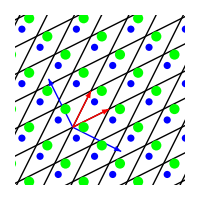

```mathematica
ClearAll[ springLatticePlot ] ;
springLatticePlot[ calcResults_List, {color_, iOff_Integer, jOff_Integer, iStartAdj_, jStartAdj_, iRangeAdj_Integer, jRangeAdj_Integer},springStrengthFraction_] := Module[{pt, pointsDataTable, numberLatticeLinesToDisplay},

{pt,numberLatticeLinesToDisplay}={"pointsDataTable","numberLatticeLinesToDisplay"} /. calcResults ;
pointsDataTable = pt[[1]] ; (*FIXME*)

ListLinePlot[
Flatten[Table[
springPoints[ pointsDataTable[[i,j]], pointsDataTable[[i+iOff,j + jOff]], Ceiling[8 springStrengthFraction] ],
{i, 1 + iStartAdj, numberLatticeLinesToDisplay[[1]] * 2 + iRangeAdj},
{j, 1 + jStartAdj, numberLatticeLinesToDisplay[[2]] * 2 + jRangeAdj}
], 2] ,
PlotStyle ->  color ]
];

ClearAll[ plotSprings ] ;
plotSprings::usage = "Example:

Module[{ld},
ld = locDependent[{1/2,1}, {1,1/2}, {{0.1,1.2} + {1/2,1} + {1,1/2}, {1.3, 0.5} - {1/2,1} - {1,1/2}}] ;
plotSprings[{10,20}, ld ] 
]
" ;
plotSprings[massValue_List, calcResults_] := Module[{latticeBasis,reciprocalBasis,pointsDataTable, numberLatticeLinesToDisplay, lines},

{latticeBasis,reciprocalBasis,pointsDataTable,numberLatticeLinesToDisplay, lines}={"latticeBasis","reciprocalBasis","pointsDataTable","numberLatticeLinesToDisplay", "lineTable"}  /. calcResults  ;

(*Show[{*)
Graphics[{
lines
,Blue,Arrow[{{0,0}, reciprocalBasis[[#]]}] & /@ Range[2]
,Thick,Arrowheads[0.05]
,Red,Arrow[{{0,0}, latticeBasis[[#]]}] & /@ Range[2]
,Blue
,PointSize[Sqrt[massValue[[1]]/mMax/500]]
,Point[ # ] & /@ pointsDataTable[[1]]
,Green
,PointSize[Sqrt[massValue[[2]]/mMax/500]]
,Point[ # ] & /@ pointsDataTable[[2]]
}
,PlotRange -> {{-windowHalfWidth/2, windowHalfWidth}, {-windowHalfWidth/2, windowHalfWidth}}
,ImageSize->primaryDisplaySize
](*,
kp1,
kp2,
kp3,
kp4*)
(*}]*)
] ;


Module[{ld},
ld = locDependent[{1/2,1}, {1,1/2}, {{0.1,1.2} + {1/2,1} + {1,1/2}, {1.3, 0.5} - {1/2,1} - {1,1/2}}] ;
plotSprings[{10,20}, ld ] 
]
```